Rupture behavior in a 1D regularized, variational, fracture model

The governing nonlinear of the system 

φ_(,ξξ)- α^2 φ  + α^2(β^2(1-φ))^-3=0

We are going to derive the stress–strain response of the 1D bar using the shooting method. These results are going to complement the results obtained by Kaushik using FEA. The goal is to cs



(i)	The spacing between the diagonal lines decreases with increasing α.

(ii)	Thus, in the limit as α⟶∞ the bands might get infinitesimally close. Thus, in the limit the σ–ϵ curve would look very similar to those 		experimentally. For example in concrete. Or such curves could be seen in plasticity models. (Perhaps we should ask David as to in what 	type of plasticty models/experimentsIt are such curves seen).

(iii)	All critical/stationary points are stable w.r.t the Legendre variations.
(iv)	We tested stability  w.r.t to the Jacobi variation using a sufficiency condition and a necessary conditions.
		Π[ϕ]=(∫_0)^1ℒ(x,ϕ,ϕ’) dξ; ϕ ∈ {W^(1,2)(0,1) | ϕ’(0)=ϕ’(1)=0}
		
where ℒ (x, ϕ, ϕ') = 1/2 ϕ'^2-α^2 ϕ^2+β^2(α^2(1-ϕ))^2. We can compute the second variation of the functional as follows, 

		Π[ϕ+ϵ δϕ]=Π[ϕ]+ϵδΠ[δϕ;ϕ]+ϵδ^2Π[δϕ;ϕ]+o(ϵ^2),

where ϵδΠ[δϕ;ϕ] and ϵ^2δ^2Π[δϕ;ϕ]  are called the first and second variations of Π at ϕ in the direction δϕ. Let ϕ^* be a stationary points. Then, we have that
		
		Π[ϕ_*+ϵ δϕ]-Π[ϕ_*]=ϵ^2 δ^2 Π[δϕ;ϕ_*]+o(ϵ^2).

The second variation as a more explicit form 
		ϵ^2 δ^2 Π[δϕ; ϕ_*]=∫P(ξ;ϕ)δϕ^2(ξ)+2Q(ξ;ϕ)δϕ(ξ) δϕ'(ξ)+R(ξ;ϕ)δϕ'^2(ξ),
		where for our functional we have that 
		P(ξ,ϕ_*)=2α^2[1-3 β^2{1-ϕ(ξ)}^-4],
Q(ξ,ϕ_*)=0,
R(ξ,ϕ_*)=2.
for all ξ∈ (0,1). In order for ϕ_* to be stable against a particular class of variations Τ𝒱 it is necessary that  ϵδ^2 Π[δϕ;ϕ_*]>0 for all δϕ ∈ T𝒱.



Jacobi variations. 

We derive necessary conditions by requiring for stability against Jacobi variations by choosing  δϕ=c, where c∈ℝ^+\0. This particular choice of δϕ implies that for ϕ_* to be stable agianst jacobi variations it is necessary that
				c^2(∫^1)_0 P(ξ,ϕ_*)dξ>0		 
		
 
A sufficient condition for ϵδ^2 Π[δϕ;ϕ_*]>0 for all  Jacobi variations is obtained by requirng that M(ξ;ϕ_*) is positive definite for all ξ∈ (0,1), where 

						M=(P | Q
P | R).

This requires that P(ξ;ϕ_*)>0  for all ξ∈ (0,1).
 
 
(iv)	We have already shown that the left branch of the Borden curve is Jacobi-stable. In this case they have to satisfy the necessary condition. Numerical calculations show that they infact satisfy the necessary condition. A stable point does not have to satisfy the sufficiency condition. However, interestingly, numerical calculations show that they also in fact satisfy the sufficiency conditions.

	We have already shown that the right branch of the Borden curve is Jacobi-unstable.   If something does not stasfy the  condition then it will aslo not satisfy the sufficiency condition, this is what we find numerically. However, the points do not necessaryly also have to not satisfy the necessary condition. However, interestingly, we find numerically that points also do not satisfy the nessary condition. 
	
	
	Numerically we found all point internal to the Borden curve do not satisfy the necessary conidtion to be Jacobi-stable. If they do not satisfy the necessary condition they will of course not satisfy the  condition. So they are unstable. They of course will also not satiafy sufficiency cond.This is what we found  numerical.	
	
	So leaving the left branch of the Borden curve everything is unstable w.r.t.Jacobi variations.

## Calculations Initialization and Module Definitions

```mathematica
(*Initialization. This cell  initialises the important variables.*)
ClearAll["Global`*"]
Cell[StyleData["Input"],FontFamily->"Helvetica Neue",FontSize->12];
c=N[√27/256];
α=√50;
(*ShootingPoints={0.0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.95};*)
ShootingPoints={0.0,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,0.999,0.9999};
```

```mathematica
(*Initialization. This cell  initialises the important variables.*)
f[βs_,αs_]:=Module[{α=αs,β=βs,sols},sols=Map[First[NDSolve[{ϕ''[ξ]-α^2 ϕ[ξ]+(β^2 α^2)/(1-ϕ[ξ])^3==0,ϕ'[0]==0,ϕ'[1]==0},ϕ,ξ, Method->"BoundaryValues"->{"Shooting", "StartingInitialConditions"->{ϕ[0] == #, ϕ'[0] == 0}},MaxSteps->1000000]]&,
ShootingPoints];
sols
(*Plot[Evaluate[ϕ[ξ] /. sols], {ξ,0,1}, PlotStyle->{Black, Blue, Green,Brown, Purple, Gray, Red, Magenta, Yellow}]*)
]



Plotϕ[ks_,solss_]:=Module[{k=ks,sols=solss},
Plot[Evaluate[ϕ[ξ]/.sols[[k,1]]],{ξ,0,1}]]



ComputeStrain[ks_,solss_,βs_]:=Module[{k=ks,sols=solss,dummy,β=βs},
dummy[ξ_]:=Evaluate[ϕ[ξ]/.sols[[k,1]]];
β*NIntegrate[1/(1-dummy[ξ])^2,{ξ,0,1}]
]

ComputePMax[ks_,solss_,βs_]:=Module[{k=ks,sols=solss,dummy,β=βs,ϕMax=0},
dummy[ξ_]=Evaluate[ϕ[ξ]/.sols[[k,1]]];
ϕMax=NMaxValue[{dummy[ξ] ,0≤ ξ ≤ 1},ξ];
1-(3 β^2)/(1-ϕMax)^4
]

ComputePInt[ks_,solss_,βs_]:=Module[{k=ks,sols=solss,dummy,β=βs,ϕMax=0},
dummy[ξ_]=Evaluate[ϕ[ξ]/.sols[[k,1]]];
NIntegrate[1-(3 β^2)/(1-dummy[ξ])^4,{ξ,0,1}]
]
```

## Calculate stationary points

```mathematica
(*Initialization*)
Clear[solnum,βVec,ϵVec];
βVec=Range[0,1,0.05]*c;
N1=Length[βVec];
N2=Length[ShootingPoints];
solnum=Range[1,N2];
solsVec=Table[0,{i,1,N1},{j,1,N2}];
ϵVec=Table[0,{i,1,N1},{j,1,N2}];
PMaxVec=Table[0,{i,1,N1},{j,1,N2}];
PIntVec=Table[0,{i,1,N1},{j,1,N2}];
```

```mathematica
For[i=0,i< N1,i++;
Clear[βi,solsi,strainsi,PMaxi,PInti];
βi=βVec[[i]];
Print[βi];
solsi=f[βi,α];
p1=Plotϕ[2,solsi];
strainsi=Map[ComputeStrain[#,solsi,βi]&,solnum];
ϵVec[[i,;;]]=strainsi;
(*PMaxi=Map[ComputePMax[#,solsi,βi]&,solnum];*)
PInti=Map[ComputePInt[#,solsi,βi]&,solnum];
PIntVec[[i,;;]]=PInti;
PMaxi=Map[ComputePMax[#,solsi,βi]&,solnum];
PMaxVec[[i,;;]]=PMaxi
]
```

0.

0.016238

NMaxValue::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

0.032476

0.0487139

0.0649519

0.0811899

0.0974279

0.113666

0.129904

0.146142

0.16238

0.178618

0.194856

0.211094

0.227332

0.24357

0.259808

0.276046

0.292284

NDSolve::mxst: Maximum number of 1000000 steps reached at the point ξ == 3.13725×10^-9.

ReplaceAll::reps: 4.271484375000001`/(1 - ϕ[« 1 »])^3 - 50 ϕ[ξ] + SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand 1 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

ReplaceAll::reps: 4.271484375000001`/(1 - ϕ[« 1 »])^3 - 50 ϕ[ξ] + SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NIntegrate::inumr: The integrand 1 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NMaxValue::nnum: The function value (ϕ[0.04573179628771076`]/. 4.271484375000001`/(1 - ϕ[« 1 »])^3 - 50 ϕ[0.04573179628771076`] + SuperscriptBox[ is not a number at {ξ} = {0.0457318}.

General::stop: Further output of NMaxValue :: nnum will be suppressed during this calculation.

0.308522

0.32476

ReplaceAll::reps: 4.271484375000001`/(1 - ϕ[« 1 »])^3 - 50 ϕ[ξ] + SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand 1/(1 - (ϕ[ξ]/. « 1 » == 0))^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

ReplaceAll::reps: 4.271484375000001`/(1 - ϕ[« 1 »])^3 - 50 ϕ[ξ] + SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand 1/(1 - (ϕ[ξ]/. « 1 » == 0))^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

ReplaceAll::reps: 4.271484375000001`/(1 - ϕ[« 1 »])^3 - 50 ϕ[ξ] + SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NIntegrate::inumr: The integrand 1/(1 - (ϕ[ξ]/. « 1 » == 0))^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

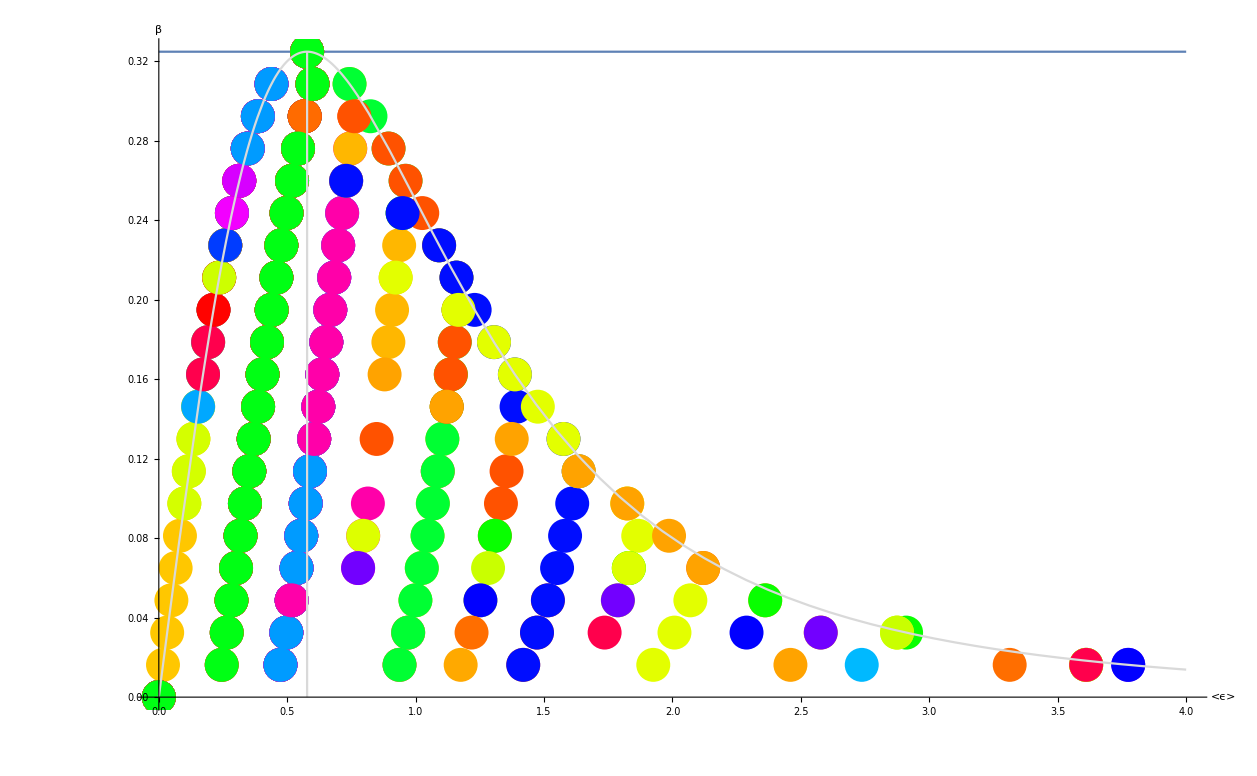

```mathematica
Clear[pold,pnew, data];
pold=Plot[c,{x,0,4}];
For[i=0,i< N2,i++;
Clear[data];
data=Reverse[Transpose[{βVec[[;;]],ϵVec[[;;,i]]}],2];
pnew=ListPlot[data,PlotStyle->Hue[Random[]]];
pold=Show[pold,pnew,PlotRange->All,AxesLabel->{
Style["<ϵ> ",Black,FontFamily->"TimesNewRoman",30],
Style["β",Black,FontFamily->"TimesNewRoman",30]},
ImageSize->400,
GridLines->None,
AxesStyle->Directive[Black,Thickness[0.001],FontFamily->"Times New Roman",18]
];
];
BordenCurve=ParametricPlot[{{ϵ̃,(ϵ̃)/((1+(ϵ̃)^2)^2)},{1/(√3),(ϵ̃)/4 c}},{ϵ̃,0,4},PlotStyle->{LightGray}];
Show[pold,BordenCurve]
```

## Stability of Stationary Points

```mathematica
(*Calculation*)
Clear[ci,cj,cnT,cnF,csT,csF,x,y,pVecNessT,pVecNessF,pVecSuffT, pVecSuffF,StabilityPlot];

pVecNessT=Table[5,{i,1,N1*N2,1},{j,1,2,1}];
pVecNessF=Table[5,{i,1,N1*N2,1},{j,1,2,1}];

pVecSuffT=Table[5,{i,1,N1*N2,1},{j,1,2,1}];
 pVecSuffF=Table[5,{i,1,N1*N2,1},{j,1,2,1}];


For[ci=0;cnT=1;cnF=1;csT=1;csF=1,ci< N1,ci++;
For[cj=0;x=0;y=0,cj<N2,cj++;
x=ϵVec[[ci,cj]];
y=βVec[[ci]];

(*Necessary conditions*)
If[PIntVec[[ci,cj]]>0,
pVecNessT[[cnT,1]]=x;
pVecNessT[[cnT,2]]=y;
cnT+=1,
pVecNessF[[cnF,1]]=x;
pVecNessF[[cnF,2]]=y;
cnF+=1];

(*Sufficiency conditions*)
If[PMaxVec[[ci,cj]]>0,
pVecSuffT[[csT,1]]=x;
pVecSuffT[[csT,2]]=y;
csT+=1,
pVecSuffF[[csF,1]]=x;
pVecSuffF[[csF,2]]=y;
csF+=1];

Clear[x,y]
]
];
```

ReplaceAll::reps: 4.271484375000001`/(1 - ϕ[« 1 »])^3 - 50 ϕ[ξ] + SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand 1/(1 - (ϕ[ξ]/. « 1 » == 0))^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

ReplaceAll::reps: 4.271484375000001`/(1 - ϕ[« 1 »])^3 - 50 ϕ[ξ] + SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand 1 - 0.256289/(1 - (ϕ[ξ]/. Plus[« 3 »] == 0))^4 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

ReplaceAll::reps: 4.271484375000001`/(1 - ϕ[« 1 »])^3 - 50 ϕ[ξ] + SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NMaxValue::nnum: The function value (ϕ[0.04573179628771076`]/. 4.271484375000001`/(1 - ϕ[« 1 »])^3 - 50 ϕ[0.04573179628771076`] + SuperscriptBox[ is not a number at {ξ} = {0.0457318}.

General::stop: Further output of NMaxValue :: nnum will be suppressed during this calculation.

NIntegrate::inumr: The integrand 1/(1 - (ϕ[ξ]/. « 1 » == 0))^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

## Plots

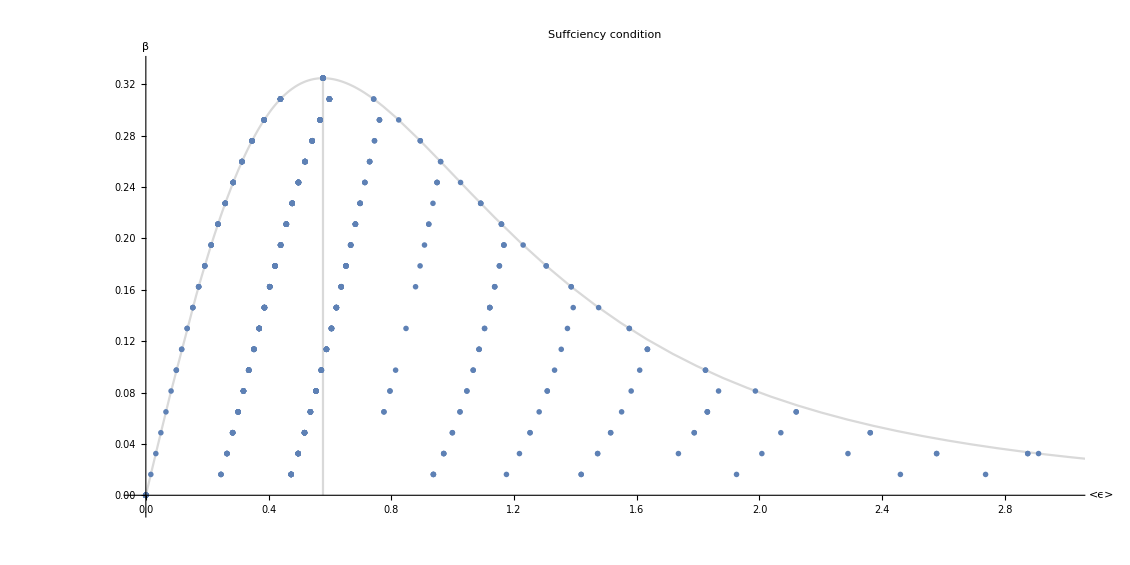

```mathematica
(*Sufficiency condition plot*)
StabilityPlotSuffT=ListPlot[{pVecSuffT},PlotMarkers->Style["T",24,Green]];
StabilityPlotSuffF=ListPlot[{pVecSuffF},PlotMarkers->Style["F",24,Red]];
StabilityPlotSuff=
Show[BordenCurve,
StabilityPlotSuffT,
StabilityPlotSuffF,
(*LegendLabel->{"B","Pass","Fail"},*)
PlotLabel->Style["Suffciency condition",Black,FontFamily->"TimesNewRoman",30],
PlotRange->{{-0.01,3},{-0.01,c+0.01}},AxesLabel->{
Style["<ϵ> ",Black,FontFamily->"TimesNewRoman",30],
Style["β",Black,FontFamily->"TimesNewRoman",30]},
AspectRatio->.5,
ImageSize->800,
GridLines->None,
AxesStyle->Directive[Black,Thickness[0.001],FontFamily->"Times New Roman",18]
]
```

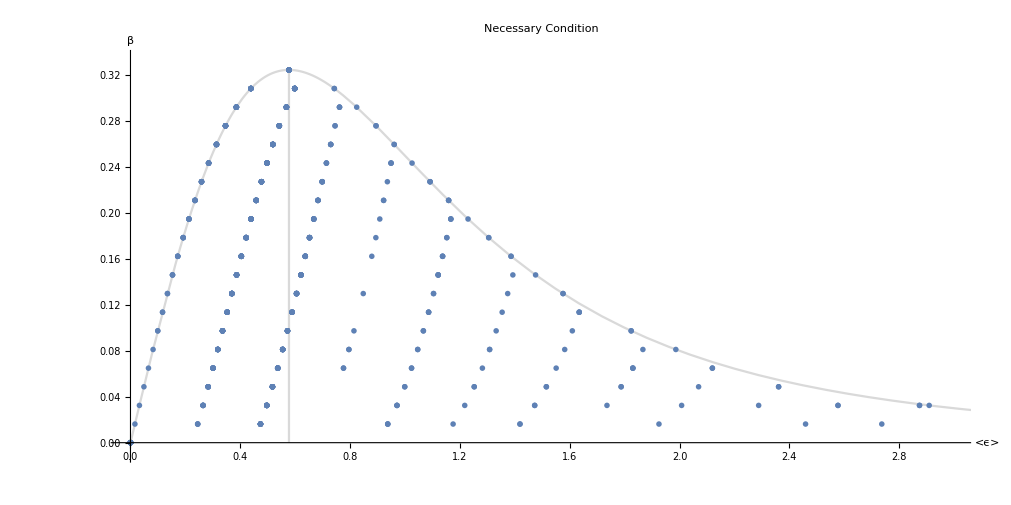

```mathematica
(*Necessary Condition Plot*)
StabilityPlotNessT=ListPlot[{pVecNessT},PlotMarkers->Style["T",24,Black]];
StabilityPlotNessF=ListPlot[{pVecNessF},PlotMarkers->Style["F",24,Gray]];
StabilityPlotNess=
Show[
BordenCurve,
StabilityPlotNessT,
StabilityPlotNessF,
PlotLabel->Style["Necessary Condition",Black,FontFamily->"TimesNewRoman",30],
PlotRange->{{-0.01,3},{-0.01,c+0.01}},
AxesLabel->{
Style["<ϵ> ",Black,FontFamily->"TimesNewRoman",30],
Style["β",Black,FontFamily->"TimesNewRoman",30]},
AspectRatio->.5,
ImageSize->800,
GridLines->None,
AxesStyle->Directive[Black,Thickness[0.001],FontFamily->"Times New Roman",18]
]
```

## Results

#### Effect of increaing α

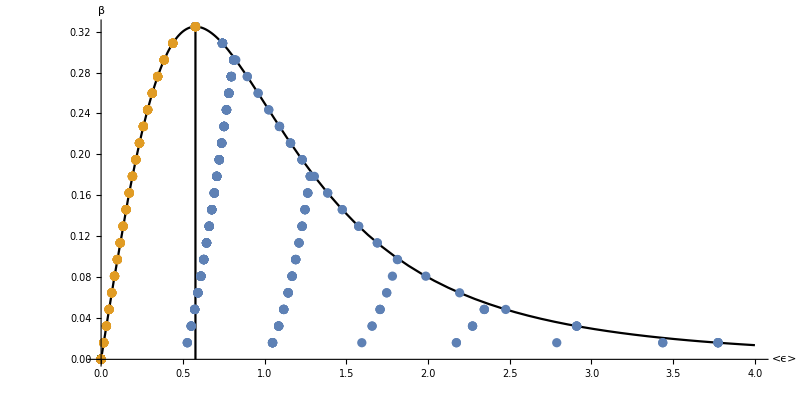
ShootingPoints={0.0,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,0.999,0.9999};
α=√10;

α=√10
-Graphics-
 I see 5/6 diagonal bands inside the σ–ϵ envelope.

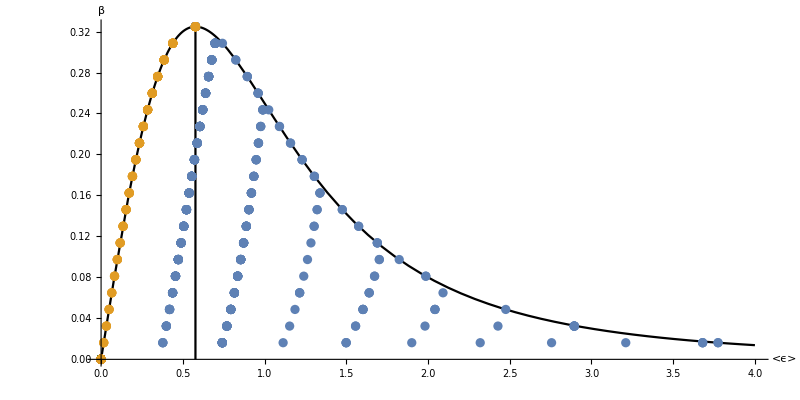
The shooting points are the same as the prvious case
α=√20
-Graphics-

I see 8 diagonal bands inside the σ–ϵ envelope.

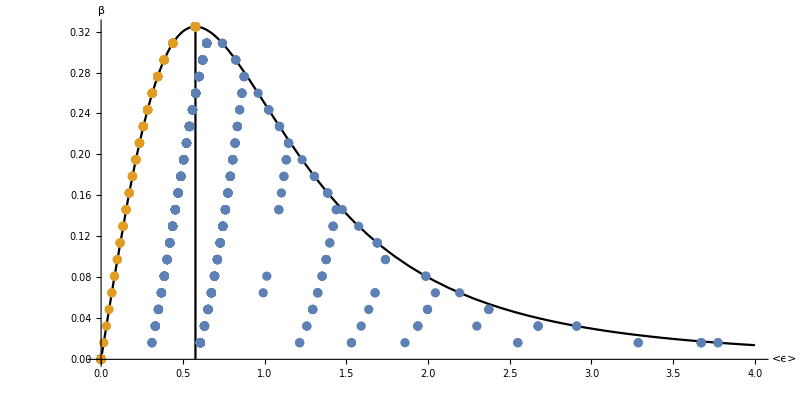
The shooting points are the same as the previous case
α=√30
-Graphics-


	1. Seems like the shooting method did not capture all the points inside the envelope of the σ–ϵ plot. This could just be because of numerical problems. 

2. I see 9 diagonal bands inside the σ–ϵ envelope.

3.

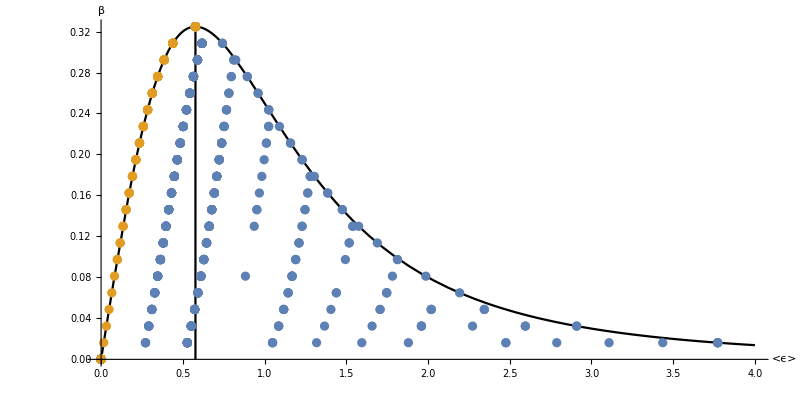
The shooting poinst are the same as before
α=√40
-Graphics-
 I see 11/12 diagonal bands inside the σ–ϵ envelope.

### Sufficient and Necessary Criteria

Notes:
Sufficiency criteria, Green=True, Red=Flase
Necessary criteria, Black=True, Gray=Flase

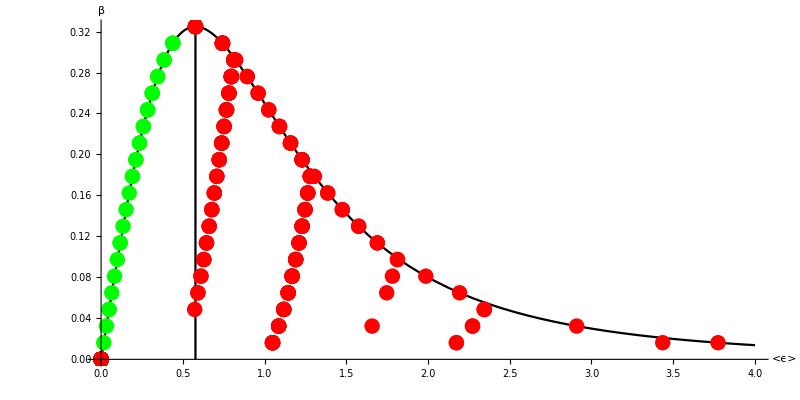
PIntCriteria=Necessary, α=√10, smaller number of shooting points.
-Graphics-

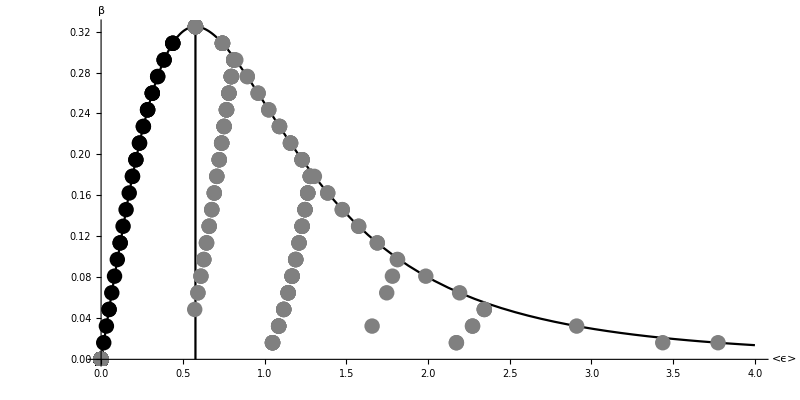
PMax riteria=Sufficency, α=√10
-Graphics-

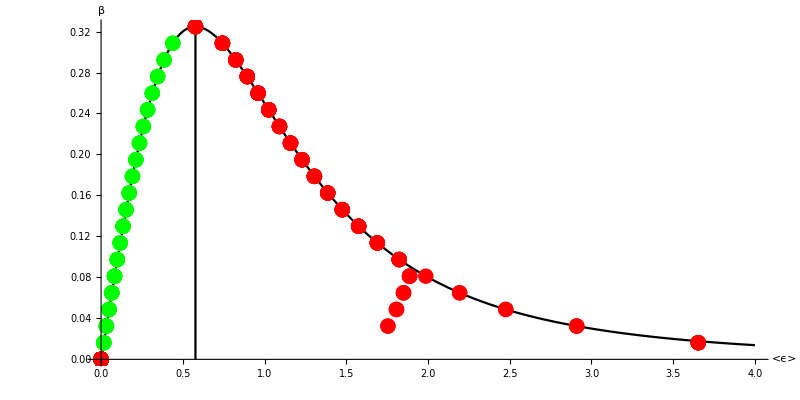
PInt criteria,Necessary,α=1 
-Graphics-

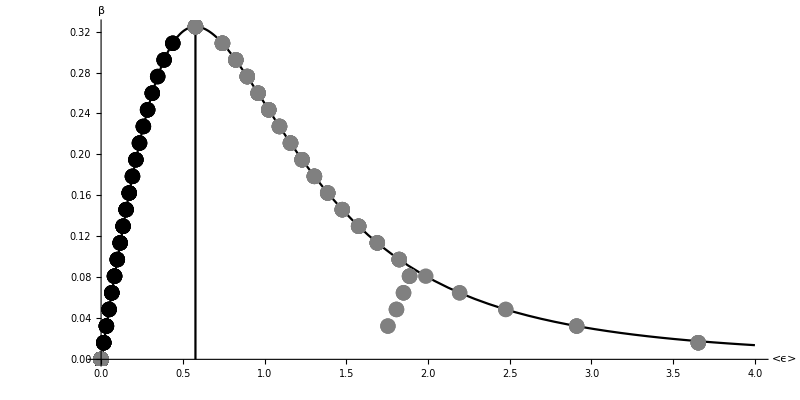
Pmax , α=1
-Graphics-

```mathematica
s
```

s